# Problem Set 1.1

## Ex 1 - a.

```mathematica
points = {{0,0,0}}
```

```mathematica
VectorPlot3D[{{1,2,3},{3,6,9}},{x,-10,10},{y,-10,10},{z,-10,10}, PlotRange->All, VectorPoints->5]
```

-Graphics3D-

## Ex. 1 - b.

```mathematica
VectorPlot3D[{{1,0,0},{0,2,3}},{x,-10,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

```mathematica
Graphics3D[InfinitePlane[{0,0,0},{{1,0,0},{0,2,3}}]]
```

-Graphics3D-

## Ex. 1 - c.

```mathematica
VectorPlot3D[{{2,0,0},{0,2,2},{2,2,3}},{x,-10,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

## Ex. 2

{0,0}

{4,1}

{-2,2}

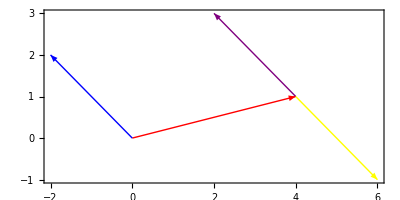

ClearAll

```mathematica
o = {0,0}
v = {4,1}
w={-2,2}
Graphics[{{Red, Arrow[{o,v}]},{Blue, Arrow[{o,w}]}, {Purple, Arrow[{v,v+w}]}, {Yellow, Arrow[{v,v-w}]}},Frame->True]
ClearAll
```

## Ex. 3

{0,0}

{{v1→3,v2→3,w1→2,w2→-2}}

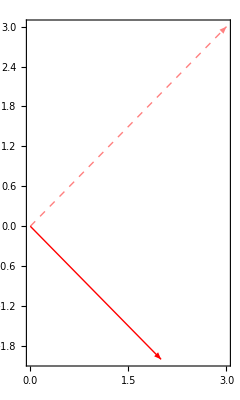

```mathematica
o={0,0}
Solve[v1+w1==5&&v1-w1==1&&v2+w2==1&&v2-w2==5]
Graphics[{{Dashed,Pink,Arrow[{o,{3,3}}]},{Red,Arrow[{o,{2,-2}}]}}, Frame->True]
v=w=.
```

## Ex. 4

```mathematica
v={2,1}
w={1,2}
Manipulate[Graphics[{{Purple,Arrow[{{0,0},v}]},{Pink,Arrow[{{0,0},w}]}, {Cyan,Arrow[{{0,0},3*v+w}]},{Green,Arrow[{{0,0},c*v+d*w}]}},Frame->True],{c,-10,10},{d,-10,10}]
```

{2,1}

{1,2}

Thread::tdlen: Objects of unequal length in 3 {0,0} {1,-2,1} cannot be combined.

Thread::tdlen: Objects of unequal length in 4.7 {0,0} {1,-2,1} cannot be combined.

## Ex. 5

```mathematica
u={1,2,3}
v={-3,1,-2}
w={2,-3,-1}
LinearSolve[u+v+w]

Graphics3D[{InfinitePlane[{0,0,0},{u,w}]},{InfinitePlane[{0,0,0},{u,v}]},{InfinitePlane[{0,0,0},{u,w}]}]
```

{1,2,3}

{-3,1,-2}

{2,-3,-1}

LinearSolve::matrix: Argument {0,0,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,0,0}]

## Ex. 6 - (*Como????????????*)

```mathematica
d=.
c=.

v1=1
v2=-2
v3=1
w1=0
w2=1
w3=-1
Solve[c*1+d*0==3&&c*(-2)+d*1==3&c*1+d*(-1)==6, {c,d}]
```

1

-2

1

0

1

-1

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-d+c (c 1+d 0==3&&c (-2)+d 1==3&)==6,{c,d}]

## Ex. 7

```mathematica
d=.
c=.
Manipulate[Graphics[{{Red, Arrow[{{0,0},{2*IntegerPart[c],IntegerPart[c]}}]},{Blue,Arrow[{{0,0},{0,IntegerPart[d]}}]}}, Frame->True],{c,0,2},{d,0,2}]
```

## Ex. 8

{4,2}

{-1,2}

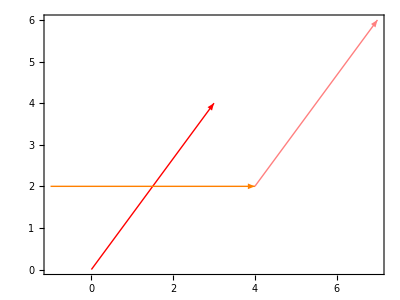

```mathematica
v={4,2}
w={-1,2}
Graphics[{{Red,Arrow[{{0,0},v+w}]},{Orange,Arrow[{w,v}]},{Pink,Arrow[{v,2*v+w}]}},Frame->True]
```

## Ex. 9 The three other corners are: {-2,2}, {4,0},{4,4}

{1,1}

{4,2}

{1,3}

{-2,2}

{}

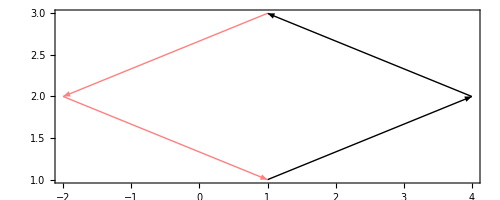

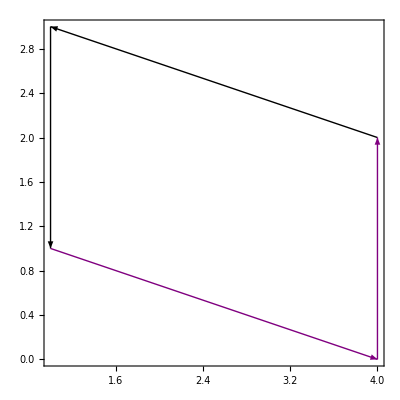

```mathematica
c=d=.
a={1,1}
b={4,2}
c={1,3}
d={-2,2}
Graphics[{{Arrow[{a,b}]},{Arrow[{b,c}]},{Pink,Arrow[{c,d}]},{Pink,Arrow[{d,a}]}},Frame->True]
Graphics[{{Arrow[{c,a}]},{Arrow[{b,c}]},{Purple,Arrow[{a,a-c+b}]},{Purple,Arrow[{a-c+b,b}]}},Frame->True]
```

## Ex. 10

```mathematica
a=b=c=.
Manipulate[Graphics3D[{{Pink,Arrow[{{0,0,0},{1,0,0}+{0,1,0}}]},{Red,Arrow[{{0,0,0},{1,0,0}+{0,1,0}+{0,0,1}}]},{Green,Arrow[{{0,0,0},a*{1,0,0}+b*{0,1,0}+c*{0,0,1}}]}},Axes->True],{a,-1,1},{b,-1,1},{c,-1,1}]
```

## Ex. 11